```mathematica
Clear["Global`*"];
```

```mathematica
NN = 201; (* количество точек в сетке, но точки в нуле у нас нет, т.к. получаем расходимость в уравнении *)
rMax = 25; (* граница окна, в котором мы работаем *)
rCore = 4.2; (* радиус жилы *)
h = rMax/NN; (* шаг дискретизации *)
λ = 1.55; (* длина волны излучения *)
nMat = 1.444; (* показатель преломления в материале *)
dn = 0.004; (* повышение показателя преломления в среде, например допируя германием *)
k0 = 2 Pi/λ; (* волновое число в ваккууме *)
l=0; (* угловой момент моды, для LP - количество Min,Max по углу Theta *)
```

```mathematica
n = Join[
Table[nMat+dn,{Floor[rCore*NN/rMax]}],
Table[nMat,{NN-Floor[rCore*NN/rMax]}]
];
ListPlot[n,Joined->True,PlotRange->All];
```

```mathematica
rHyperbolic = Table[1./i, {i, h, rMax,h}];
ListPlot[rHyperbolic,Joined->True,PlotRange->All];
```

```mathematica
DMatrix=
DiagonalMatrix[ConstantArray[0.5/h,NN-1],1]+
DiagonalMatrix[ConstantArray[-0.5/h,NN-1],-1];
DMatrix[[1,;;3]] = {-1.5,2.,-0.5}/h;
DMatrix[[NN,-3;;]] = {0.5,-2.,1.5}/h;
DMatrix[[-5;;,-5;;]]//MatrixForm;
ListPlot[DMatrix.Table[i*h,{i,1,NN}],Joined->True,PlotRange->All];
```

```mathematica
D2Matrix=
DiagonalMatrix[ConstantArray[1./h^2,NN-1],1]+
DiagonalMatrix[ConstantArray[-2/h^2,NN],0]+
DiagonalMatrix[ConstantArray[1./h^2,NN-1],-1];
D2Matrix [[1,;;4]]={2.,-5.,4.,-1.}/h^2;
D2Matrix [[NN,-4;;]]={-1.,4.,-5.,2.}/h^2;
D2Matrix[[;;5,;;5]]//MatrixForm;
ListPlot[{DMatrix.Table[(i*h)^2,{i,1,NN}],D2Matrix.Table[(i*h)^2,{i,1,NN}]},Joined->True,PlotRange->All];
```

```mathematica
besselOperator = D2Matrix+rHyperbolic*DMatrix+k0^2*n^2*IdentityMatrix[NN]-l^2*rHyperbolic^2*IdentityMatrix[NN];
besselOperator[[;;10,;;10]]//MatrixForm;
```

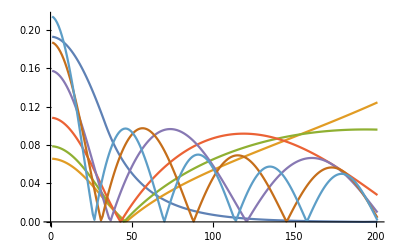

```mathematica
{Evalues,Evectors} = Eigensystem[besselOperator];
modes = Chop[Select[Sqrt[Evalues/k0^2],(Abs[Im[#]]≤10^-4 && nMat≤ Re[#] && nMat+dn ≥ Re[#])& ]];
ListPlot[Abs[Evectors[[130;;136]]],Joined->True,PlotRange->All]
```